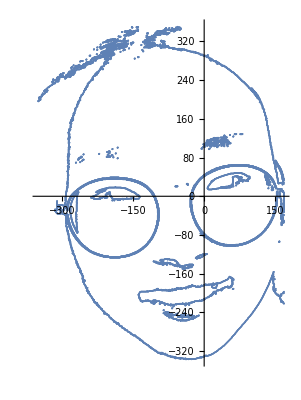

```mathematica
imgImport = Import["/Users/lsqyRobot/Desktop/girl.png"];
compute[pts_,m_]:=Block[{z,cn,r,theta,index,tab,p,circles},z=pts[[All,1]]+I*pts[[All,2]];
cn=cf[z,m];
r=Abs/@cn;
theta=Arg/@cn;
index={m+1}~Join~Riffle[Range[m+2,2 m+1],Reverse[Range[1,m]]];
tab=Table[toPt[cn[[j]]*Exp[I*(j-m-1)*t]],{j,index}];
p[t_]=Accumulate@tab;
circles[t_]=Circle@@@Transpose[{p[t],r[[index]]}][[;;2 m+1]];
{p[t],circles[t]}]
img=Binarize[imgImport~ColorConvert~"Grayscale"~ImageResize~520~Blur~0,0.4];
img=DeleteSmallComponents@img;
pts=DeleteDuplicates@Flatten[Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{0.5}],_Line,-1][[All,1]],1];
center=Mean@MinMax[pts]&/@Transpose@pts;
pts=#-center&/@pts;
plot=ListPlot[pts,AspectRatio->Automatic,PlotRange->Full]
```

```mathematica
shortest=Last@FindShortestTour@pts;
pts=pts[[shortest]];
```

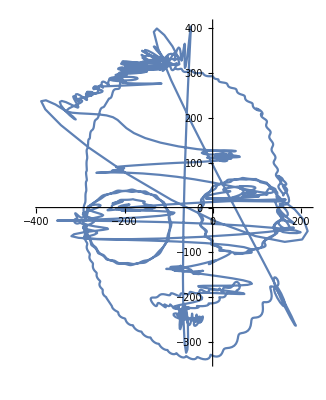

```mathematica
SetAttributes[toPt,Listable]
toPt[z_]:=ComplexExpand[{Re@z,Im@z}]//Chop;
cf=Compile[{{z,_Complex,1}},Module[{n=Length@z},1/n*Table[Sum[z[[k]]*Exp[-I*i*k*2 Pi/n],{k,1,n}],{i,-m,m}]]];
z=pts[[All,1]]+I*pts[[All,2]];
m=300;
cn=cf[z];
{f[t_],g[t_]}=Sum[cn[[j]]*Exp[I*(j-m-1)*t],{j,1,2 m+1}]//toPt;
ParametricPlot[{f[t],g[t]},{t,0,2 Pi}]
```

```mathematica
r=Abs/@cn;
theta=Arg/@cn;
index={m+1}~Join~Riffle[Range[m+2,2 m+1],Reverse[Range[1,m]]];
p[t_]=Accumulate@Table[cn[[j]]*Exp[I*(j-m-1)*t],{j,index}]//toPt;
circles[t_]=Table[Circle[p[t][[i-1]],r[[index[[i]]]]],{i,2,2 m+1}];
```

```mathematica
anims=ParallelTable[ParametricPlot[{f[s],g[s]},{s,0,t},AspectRatio->Automatic,Epilog->{circles[t],Line[p[t]],Point[p[t]]},PlotRange->{{-400,400},{-400,300}},ImageSize->400],{t,Subdivide[0.1,4 Pi,100]}];
ListAnimate@anims
```